```mathematica
P = Array[Sqrt[#]&,100,{-3,3}]//N
```

{0.+1.73205 ⅈ,0.+1.71447 ⅈ,0.+1.6967 ⅈ,0.+1.67874 ⅈ,0.+1.6606 ⅈ,0.+1.64225 ⅈ,0.+1.62369 ⅈ,0.+1.60492 ⅈ,0.+1.58592 ⅈ,0.+1.5667 ⅈ,0.+1.54724 ⅈ,0.+1.52753 ⅈ,0.+1.50756 ⅈ,0.+1.48732 ⅈ,0.+1.4668 ⅈ,0.+1.446 ⅈ,0.+1.42489 ⅈ,0.+1.40346 ⅈ,0.+1.3817 ⅈ,0.+1.35959 ⅈ,0.+1.33712 ⅈ,0.+1.31426 ⅈ,0.+1.29099 ⅈ,0.+1.2673 ⅈ,0.+1.24316 ⅈ,0.+1.21854 ⅈ,0.+1.19342 ⅈ,0.+1.16775 ⅈ,0.+1.1415 ⅈ,0.+1.11464 ⅈ,0.+1.08711 ⅈ,0.+1.05887 ⅈ,0.+1.02986 ⅈ,0.+1. ⅈ,0.+0.969223 ⅈ,0.+0.937437 ⅈ,0.+0.904534 ⅈ,0.+0.870388 ⅈ,0.+0.834847 ⅈ,0.+0.797724 ⅈ,0.+0.758787 ⅈ,0.+0.717741 ⅈ,0.+0.6742 ⅈ,0.+0.627646 ⅈ,0.+0.57735 ⅈ,0.+0.522233 ⅈ,0.+0.460566 ⅈ,0.+0.389249 ⅈ,0.+0.301511 ⅈ,0.+0.174078 ⅈ,0.174078,0.301511,0.389249,0.460566,0.522233,0.57735,0.627646,0.6742,0.717741,0.758787,0.797724,0.834847,0.870388,0.904534,0.937437,0.969223,1.,1.02986,1.05887,1.08711,1.11464,1.1415,1.16775,1.19342,1.21854,1.24316,1.2673,1.29099,1.31426,1.33712,1.35959,1.3817,1.40346,1.42489,1.446,1.4668,1.48732,1.50756,1.52753,1.54724,1.5667,1.58592,1.60492,1.62369,1.64225,1.6606,1.67874,1.6967,1.71447,1.73205}

```mathematica
F[p_]:=p*I*Cot[p*I]
```

```mathematica
L = Table[F[p],{p,P}]
```

{-0.281747+0. ⅈ,-0.248026+0. ⅈ,-0.214755+0. ⅈ,-0.181924+0. ⅈ,-0.149521+0. ⅈ,-0.117537+0. ⅈ,-0.0859602+0. ⅈ,-0.0547816+0. ⅈ,-0.0239914+0. ⅈ,0.00641946+0. ⅈ,0.0364601+0. ⅈ,0.066139+0. ⅈ,0.0954646+0. ⅈ,0.124445+0. ⅈ,0.153088+0. ⅈ,0.181401+0. ⅈ,0.209392+0. ⅈ,0.237068+0. ⅈ,0.264436+0. ⅈ,0.291501+0. ⅈ,0.318272+0. ⅈ,0.344755+0. ⅈ,0.370954+0. ⅈ,0.396877+0. ⅈ,0.422529+0. ⅈ,0.447917+0. ⅈ,0.473044+0. ⅈ,0.497917+0. ⅈ,0.522541+0. ⅈ,0.54692+0. ⅈ,0.571061+0. ⅈ,0.594966+0. ⅈ,0.618642+0. ⅈ,0.642093+0. ⅈ,0.665322+0. ⅈ,0.688334+0. ⅈ,0.711134+0. ⅈ,0.733725+0. ⅈ,0.756112+0. ⅈ,0.778297+0. ⅈ,0.800286+0. ⅈ,0.82208+0. ⅈ,0.843685+0. ⅈ,0.865104+0. ⅈ,0.886339+0. ⅈ,0.907394+0. ⅈ,0.928272+0. ⅈ,0.948977+0. ⅈ,0.969512+0. ⅈ,0.989879+0. ⅈ,1.01008+0. ⅈ,1.03012+0. ⅈ,1.05+0. ⅈ,1.06973+0. ⅈ,1.0893+0. ⅈ,1.10872+0. ⅈ,1.12799+0. ⅈ,1.14711+0. ⅈ,1.16609+0. ⅈ,1.18493+0. ⅈ,1.20363+0. ⅈ,1.2222+0. ⅈ,1.24063+0. ⅈ,1.25892+0. ⅈ,1.27709+0. ⅈ,1.29512+0. ⅈ,1.31304+0. ⅈ,1.33082+0. ⅈ,1.34848+0. ⅈ,1.36603+0. ⅈ,1.38345+0. ⅈ,1.40076+0. ⅈ,1.41795+0. ⅈ,1.43502+0. ⅈ,1.45199+0. ⅈ,1.46884+0. ⅈ,1.48559+0. ⅈ,1.50223+0. ⅈ,1.51876+0. ⅈ,1.53519+0. ⅈ,1.55152+0. ⅈ,1.56774+0. ⅈ,1.58387+0. ⅈ,1.59989+0. ⅈ,1.61582+0. ⅈ,1.63166+0. ⅈ,1.6474+0. ⅈ,1.66304+0. ⅈ,1.6786+0. ⅈ,1.69406+0. ⅈ,1.70944+0. ⅈ,1.72473+0. ⅈ,1.73993+0. ⅈ,1.75504+0. ⅈ,1.77007+0. ⅈ,1.78502+0. ⅈ,1.79988+0. ⅈ,1.81466+0. ⅈ,1.82936+0. ⅈ,1.84398+0. ⅈ}

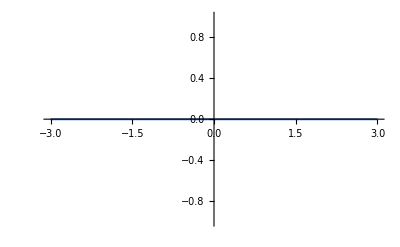

```mathematica
Plot[Im[F[p]],{p,-3,3}]
```

```mathematica
Pl
```

```mathematica
F1[p_]:= Gamma[1-2*I*p]*BesselJ[-2*I*p,2]
```

```mathematica
PCOT[p_]:= ((F1[-p]-F1[p])/(2*I*p*F1[p]) )^-1+I*p
```

```mathematica
PCOT[Sqrt[-1]]//N
```

PCOT[0.+1. ⅈ]

```mathematica
T[p_]:=-4*π*(F1[-p]-F1[p])/(2*I*p*F1[p])
```

```mathematica
T[Sqrt[-3]]//N
```

3.68349

```mathematica
Residue[V[q0,k]V[k,q0],{k,(0.-1. ⅈ)+q0}]
```

```mathematica
((9.869604401089358+0. ⅈ) ((0.-1. ⅈ)+(3.+0. ⅈ) q0+(0.+1. ⅈ) q0^2))/(((0.-1. ⅈ) q0+q0^2)^3)/.{q0->Sqrt[-1.1]}
```

0.-76988.1 ⅈ

```mathematica
-(0.+3.141592653589793 ⅈ)/((0.-1. ⅈ) q0+q0^2)
```

0.-12.5664 ⅈ

```mathematica
(2*π*I/(2*π^2))Residue[V[q0,k]*k^2/(k^2 - q0^2)*V[k,q0],{k,(0.-1. ⅈ)+q0}]
```

```mathematica
-((0.+3.141592653589793 ⅈ) (0.25+(0.+1.5 ⅈ) q0-3. q0^2-(0.+2.75 ⅈ) q0^3+1. q0^4))/(q0^3 ((0.-1. ⅈ)+q0)^2 ((0.-0.5 ⅈ)+1. q0)^2)/.{q0->Sqrt[-1.1]}
```

53.6624+0. ⅈ

```mathematica
-((0.+3.141592653589793 ⅈ) (0.25+(0.+1.5 ⅈ) q0-3. q0^2-(0.+2.75 ⅈ) q0^3+1. q0^4))/(q0^3 ((0.-1. ⅈ)+q0)^2 ((0.-0.5 ⅈ)+1. q0)^2)/.{q0->Sqrt[-3]}
```

53.6624+0. ⅈ

```mathematica
-(9.869604401089358 (0.25+(0.+1.5 ⅈ) q0-3. q0^2-(0.+2.75 ⅈ) q0^3+1. q0^4))/(q0^3 ((0.-1. ⅈ)+q0)^2 ((0.-0.5 ⅈ)+1. q0)^2)/.{q0->Sqrt[-1.1]}
```

```mathematica
0.-168.58527304504278 ⅈ/(2*π)
```

```mathematica
(9.869604401089358 ((0.+0.25 ⅈ)-1.25 q0-(0.+1.75 ⅈ) q0^2+1. q0^3))/(q0^3 ((0.-0.5 ⅈ)+1. q0)^2 ((0.-1. ⅈ)+1. q0))/.{q0->Sqrt[-1.1]}
```

0.+168.585 ⅈ

```mathematica
eps = 0
```

0

```mathematica
V[Sqrt[-1.1],0.0004999999375000273+0.048808723170190645 ⅈ]
```

5.79793×10^18-5.65979×10^20 ⅈ

```mathematica
V[p_,k_]:=(-8*π)/((p^2+k^2+2*p*k + 1)(p^2+k^2-2*p*k + 1))
```

```mathematica
(2*π*I/(2*π^2))Residue[V[q0,q]*q^2/(q^2 - q0^2)*V[q,k]*k^2/(k^2 - q0^2)*V[k,q0],{k,(0.-1. ⅈ)+q0}]
```

0

```mathematica
Solve[1/V[q0,k]==0,k]//N
```

```mathematica
{{k->0.5 ((-0.0009999998749998398+2.0000002499999225 ⅈ)-2. q0)},{k->0.5 ((0.0009999998749998398-2.0000002499999225 ⅈ)-2. q0)},{k->0.5 ((-0.0009999998749998398+2.0000002499999225 ⅈ)+2. q0)},{k->0.5 ((0.0009999998749998398-2.0000002499999225 ⅈ)+2. q0)}}/.{q0->Sqrt[-1.1]}
```

{{k→-0.0005-0.0488087 ⅈ},{k→0.0005-2.04881 ⅈ},{k→-0.0005+2.04881 ⅈ},{k→0.0005+0.0488087 ⅈ}}

```mathematica
{{k->(0.-1. ⅈ)-1. q0},{k->(0.+1. ⅈ)-1. q0},{k->(0.-1. ⅈ)+q0},{k->(0.+1. ⅈ)+q0}}/.{q0->Sqrt[-0.5]}
```

{{k→0.-1.70711 ⅈ},{k→0.+0.292893 ⅈ},{k→0.-0.292893 ⅈ},{k→0.+1.70711 ⅈ}}

```mathematica
{{k->(0.-1. ⅈ)-1. q0},{k->(0.+1. ⅈ)-1. q0},{k->(0.-1. ⅈ)+q0},{k->(0.+1. ⅈ)+q0}}/.{q0->Sqrt[-1.1]}
```

{{k→0.-2.04881 ⅈ},{k→0.-0.0488088 ⅈ},{k→0.+0.0488088 ⅈ},{k→0.+2.04881 ⅈ}}

```mathematica
k^2/(k^2 - q0^2)/.{k->0.04880884817015163 ⅈ,q0->Sqrt[-1.1]}
```

-0.00217043+0. ⅈ

```mathematica
V[Sqrt[-0.5],Sqrt[-0.5]]
```

25.1327+0. ⅈ

-1.+0. ⅈ

```mathematica
F2[p_]:=1/(2*I)Log[F1[-p]/F1[p]]
```

```mathematica
F2[Sqrt[-1.1]]//N
```

0.-0.979585 ⅈ

```mathematica
ArcTan[F3[Sqrt[-0.5]]]//N
```

7.05517×10^-33-0.500501 ⅈ

```mathematica
Sqrt[-0.99]*Cot[F2[Sqrt[-0.99]]]//N
```

-0.954199-4.89281×10^-18 ⅈ

```mathematica
F2[Sqrt[-1.0]]
```

(-ⅈ) ∞

```mathematica
F1[-Sqrt[-0.999999999999]]
```

-3.5281×10^11-0.0000432067 ⅈ

```mathematica
F1[Sqrt[-1]]//N
```

0.705668

```mathematica
1/(2*I)Log[F1[-Sqrt[-0.9999]]/F1[Sqrt[-0.9999]]]
```

1.5708-4.25838 ⅈ

```mathematica
Solve[(1 + I*k)/(1 - I*k)==S,k]
```

{{k→-(ⅈ (-1+S))/(1+S)}}

```mathematica
-(ⅈ (-1+S))/(1+S)/.{S-> fpm/fp}
```

```mathematica
FullSimplify[-(ⅈ (-1+fpm/fp))/(1+fpm/fp)]
```

(ⅈ (fp-fpm))/(fp+fpm)

```mathematica
F3[p_]:= (ⅈ (F1[p]-F1[-p]))/(F1[p]+F1[-p])
```

```mathematica
F3[Sqrt[-1]]//N
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
ArcTan[F3[Sqrt[3]]]//N
```

0.261681+0. ⅈ

```mathematica
-3.49392704466699 + π
```

```mathematica
Sqrt[-1.1204]
```

0.+1.05849 ⅈ

```mathematica
Sqrt[-1]
```

ⅈ

```mathematica
0.05849
```

```mathematica
Exp[2*I*(ⅈ) ∞]
```

0

```mathematica
Exp[2*-∞]
```

0

```mathematica
Cot[(ⅈ) ∞]
```

-ⅈ

```mathematica
F2[p_]:=(F1[-p]-F1[p])/(2*I*p*F1[p])
```

```mathematica
F2[Sqrt[0.1]]//N
```

1.53285+1.19338 ⅈ

```mathematica
1.532854268512391*-4*π
```

-19.2624

```mathematica
SMAT[p_]:= F1[-p]/F1[p]
```

```mathematica
SMAT[Sqrt[1]]//N
```

0.697543+0.716543 ⅈ

```mathematica
Sqrt[3]*Cot[F3[Sqrt[3]]]//N
```

6.31178+0. ⅈ

```mathematica
F4[p_]:=1/(2*I)Log[F1[-p]/F1[p]]
```

```mathematica
F4[Sqrt[3]]
```

```mathematica
(-8*π)/(p^2+k^2+2*p*k + 1 )/.{p->q0}
```

```mathematica
-(8 π)/(1+k^2+2 k q0+q0^2)/.{q0-> Sqrt[-1.1],k-> Sqrt[-1.1]-I}
```

122.74+0. ⅈ

```mathematica
□
```

```mathematica
-8*π/(p^2+k^2-2*p*k + 1)/.{p->q0}
```

-(8 π)/(1+k^2-2 k q0+q0^2)

```mathematica
-(8 π)/(1+k^2-2 k q0+q0^2)/.{q0-> Sqrt[-1.1],k-> Sqrt[-1.1]-I}
```

-2.26376×10^17+0. ⅈ

```mathematica
122.73967438872876*122.73967438872876*k^2/(k^2 - q0^2)
```

```mathematica
(15065.027669051158 k^2)/(k^2-q0^2)/.{q0-> Sqrt[-1.1],k-> Sqrt[-1.1]-I}
```

-32.6976+0. ⅈ

```mathematica
Sqrt[-0.5]
```

0.+0.707107 ⅈ

```mathematica
Integrate[V[q0,q]*q^2/(q^2 - q0^2)*Integrate[V[q,k]*k^2/(k^2 - q0^2)*V[k,q0],{k,0,∞}],{q,0,∞}]
```

∫_0^∞ ConditionalExpression[(128 ⅈ π^4 q (1+(q+q0) (q+4 q0)))/(q0 (q+q0) (-ⅈ+q+q0) (ⅈ+q+q0) (-2 ⅈ+q+q0) (2 ⅈ+q+q0) (-ⅈ+2 q0) (ⅈ+2 q0) (q^2-q0^2) (1+q^2-2 q q0+q0^2) (1+q^2+2 q q0+q0^2)), Im[q]>1&&Im[q0]>1]ⅆq

```mathematica
Integrate[V[q,k]*k^2/(k^2 - q0^2)*V[k,q0],{k,0,∞}]
```

ConditionalExpression[-(16 ⅈ π^3 (1+(q+q0) (q+4 q0)))/(q q0 (q+q0) (-ⅈ+q+q0) (ⅈ+q+q0) (-2 ⅈ+q+q0) (2 ⅈ+q+q0) (-ⅈ+2 q0) (ⅈ+2 q0)), Im[q]>1&&Im[q0]>1]

```mathematica
Integrate[V[q0,q]*q^2/(q^2 - q0^2)*-(16 ⅈ π^3 (1+(q+q0) (q+4 q0)))/(q q0 (q+q0) (-ⅈ+q+q0) (ⅈ+q+q0) (-2 ⅈ+q+q0) (2 ⅈ+q+q0) (-ⅈ+2 q0) (ⅈ+2 q0)),{q,0,∞}]
```

ConditionalExpression[-(4 ⅈ π^4 (-108+168 π q0-264 q0^2+774 π q0^3+768 q0^4+432 π q0^5+384 q0^6+96 π q0^7-6 q0 (-2+9 q0^2+72 q0^4+16 q0^6) ArcTan[2/q0]-12 q0 (-19+37 q0^2+72 q0^4+16 q0^6) ArcTan[q0]+54 Log[-q0]+564 q0^2 Log[-q0]+240 q0^4 Log[-q0]-54 Log[q0]+462 q0^2 Log[q0]+2052 q0^4 Log[q0]+2112 q0^6 Log[q0]+576 q0^8 Log[q0]-544 q0^2 Log[1+q0^2]-1248 q0^4 Log[1+q0^2]-960 q0^6 Log[1+q0^2]-256 q0^8 Log[1+q0^2]+31 q0^2 Log[4+q0^2]+102 q0^4 Log[4+q0^2]-96 q0^6 Log[4+q0^2]-32 q0^8 Log[4+q0^2]))/(3 q0 (1+4 q0^2)^2 (q0+4 q0^3) (9+13 q0^2+4 q0^4)), ]

```mathematica
FullSimplify[-((4 ⅈ π^4 (-108+168 π q0-264 q0^2+774 π q0^3+768 q0^4+432 π q0^5+384 q0^6+96 π q0^7-6 q0 (-2+9 q0^2+72 q0^4+16 q0^6) ArcTan[2/q0]-12 q0 (-19+37 q0^2+72 q0^4+16 q0^6) ArcTan[q0]+54 Log[-q0]+564 q0^2 Log[-q0]+240 q0^4 Log[-q0]-54 Log[q0]+462 q0^2 Log[q0]+2052 q0^4 Log[q0]+2112 q0^6 Log[q0]+576 q0^8 Log[q0]-544 q0^2 Log[1+q0^2]-1248 q0^4 Log[1+q0^2]-960 q0^6 Log[1+q0^2]-256 q0^8 Log[1+q0^2]+31 q0^2 Log[4+q0^2]+102 q0^4 Log[4+q0^2]-96 q0^6 Log[4+q0^2]-32 q0^8 Log[4+q0^2]))/(3 q0 (1+4 q0^2)^2 (q0+4 q0^3) (9+13 q0^2+4 q0^4)))]
```

-1/(3 q0^2 (1+q0^2) (1+4 q0^2)^3 (9+4 q0^2))4 ⅈ π^4 (-6 q0 (-2+9 q0^2+72 q0^4+16 q0^6) ArcTan[2/q0]+6 ((1+4 q0^2) (-18+q0 (4 q0 (7+4 q0^2)+π (28+17 q0^2+4 q0^4)))-2 q0 (1+q0^2) (-19+56 q0^2+16 q0^4) ArcTan[q0]+(9+94 q0^2+40 q0^4) Log[-q0]+(1+q0^2) (1+2 q0^2) (9+4 q0^2) (-1+12 q0^2) Log[q0])-32 q0^2 (1+q0^2) (17+22 q0^2+8 q0^4) Log[1+q0^2]-q0^2 (1+4 q0^2) (-31+22 q0^2+8 q0^4) Log[4+q0^2])

```mathematica
3 q0^2 (1+q0^2) (1+4 q0^2)^3 (9+4 q0^2)
```